```mathematica
Quit[]
```

```mathematica
(*Constants*)

(*properties of incident plain wave*)
p0 = 1 ;  (*Pa*)
θ = π/36 ; (*rad*)
(*f = 2900; (*Hz*)*)

(*properties of the envirenment (air)*)
c0 = 343 ; (*m/s*)
ρ0 = 1.25; (*kg/m^3*)
η0 = 17.8 10^-6; (*Pa s*)

(*properties of circular cylinder and the configuration*)
a = 4.00  10^-2;(*outer radious*)
h = 0.05 10^-2;(*thickness*)
b = a-h ;  (*inner radious*)
d = 11.0 10^-2; (*distance of Cylinders*)
r0 = 0.25 10^-3;  (*radious of perforation*)
σ = 14.5/100; (*%*) (*filling fraction*)
(*NoCylinder = 31;(*number of cylinders*)*)

(*fundamental relations*)
k[f_] :=(2π f)/c0 ;(*rad/m*)(*wave number*)
ω[f_] := 2π f ; (*rad/s*)(*angular frequency*)
v0 = p0/(ρ0 c0); (*speed of incident wave*)
I0 = (p0 v0)/2; (*initial intensity*)


(*impedance*)
Zp[f_] := (-ⅈ ω[f] ρ0)/σ(h+(16 r0)/(3π)(1-2.5 Sqrt[σ/π])) ; (*kg/(m^2.s)*)

(*calculation properties*)
(*nValue = 5; (*to show to what range we are calculating. mostly its good to 4*)*)
NoCylinderFrom0[n_] := (n - 1)/2 ;
nVal = 100; (*for plane field*)
nValue = 10; (*for scattered field*)
```

```mathematica
(*functions*)

(*Boundary condition constant*)
S[n_,a_,b_,f_] := (HankelH1[n, k[f] a]-(D[HankelH1[n, r],r]/. r->(k[f]a))((ⅈ Zp[f])/(ρ0 c0)+BesselJ[n, k[f]b]/(D[BesselJ[n,  r],r]/. r->(k[f]b))))/(BesselJ[n, k[f] a] - (D[BesselJ[n, r],r]/. r->(k[f]a))((ⅈ Zp[f])/(ρ0 c0)+BesselJ[n, k[f] b]/(D[BesselJ[n, r],r]/. r->(k[f]b))))

(*the equation that should be solved numerically*)
eq[n_,t_,f_] :=S[n,a,b,f]B[t,n,f]+ ∑_(l=-Num)^(t-1) ∑_(m=-nValue)^nValue ⅈ^((n-m)Sign[t-l])HankelH1[n-m, k[f] Abs[t-l]d]B[l,m, f] + ∑_(l=t+1)^Num ∑_(m=-nValue)^nValue ⅈ^((n-m)Sign[t-l])HankelH1[n-m, k[f] Abs[t-l]d]B[l,m,f]+ p0 ⅈ^n ⅇ^(-ⅈ n θ) ;

(*change of coordinate dependent on l*)
ϕl[r_,ϕ_, l_] := ArcCos[(r Cos[ϕ])/rl[r,ϕ,l]]
rl[r_,ϕ_, l_] := Sqrt[r^2+(l d)^2-2l d r Sin[ϕ]]

(*Pressure field in polar coordinates*)
PR[r_, ϕ_,f_]:= p0 ∑_(n=-nVal)^nVal ⅈ^n BesselJ[n, k[f] r] ⅇ^(ⅈ n (ϕ - θ))
VR[r_, ϕ_,f_]:=-ⅈ/(ω[f]ρ0)(D[PR[t,ϕ,f], t])/.t->r
PscR[r_,ϕ_,f_]:= ∑_(l=-Num)^Num ∑_(n=-nValue)^nValue B[l,n,f]HankelH1[n,k[f] rl[r,ϕ,l]] ⅇ^(ⅈ n ϕl[r,ϕ,l])
VscR[r_, ϕ_,f_]:=-ⅈ/(ω[f]ρ0)(D[PscR[t,ϕ,f], t])/.t->r
PtotR[r_, ϕ_,f_]:= p0 ∑_(n=-nVal)^nVal ⅈ^n BesselJ[n, k[f] r] ⅇ^(ⅈ n (ϕ - θ)) +∑_(l=-Num)^Num ∑_(n=-nValue)^nValue B[l,n,f]HankelH1[n,k[f] rl[r,ϕ,l]] ⅇ^(ⅈ n ϕl[r,ϕ,l])
VtotR[r_, ϕ_,f_]:=-ⅈ/(ω[f]ρ0)(D[PtotR[t,ϕ,f], t])/.t->r
(*Transmission Coofficent
TR[f_] :=  1/normi[f] Re[NIntegrate[PtotR[r, ϕ,f]*Conjugate[VtotR[r, ϕ,f]],{ϕ,-Num d,Num d}]]*)

(*PscComplicated[r_, l_, ϕ_,f_]:= Re[∑_(n=-nValue)^nValue (B[l,n,f]HankelH1[n,k[f] r] ⅇ^(ⅈ n ϕ) + ∑_(j=-Num)^(l-1) B[j,n,f] ∑_(m=-nValue)^nValue ⅈ^((n+m)Sign[l-j])BesselJ[n+m,k[f] Abs[l-j] d] HankelH1[m, k[f] r] ⅇ^(ⅈ m (π - ϕ))+∑_(j=l+1)^Num B[j,n,f] ∑_(m=-nValue)^nValue ⅈ^((n+m)Sign[l-j])BesselJ[n+m,k[f] Abs[l-j] d] HankelH1[m, k[f] r] ⅇ^(ⅈ m (π - ϕ)))]*)

(*changing the coordinates*)
R[x_,y_,l_] := Sqrt[x^2+(y-l d)^2] ;
ϕ[x_,y_,l_] := ArcTan[(y-l d)/x];

(*redefine the incident and scattered field in cortezian coordinates*)
P[x_, y_,f_]:= p0 ∑_(n=-nVal)^nVal ⅈ^n BesselJ[n, k[f] R[x,y,0]] ⅇ^(ⅈ n (ϕ[x,y,0]- θ))
Psc[x_,y_,f_]:= ∑_(l=-Num)^Num ∑_(n=-nValue)^nValue B[l,n,f]HankelH1[n,k[f]R[x,y,l]] ⅇ^(ⅈ n ϕ[x,y,l])

(*total pressure field*)
Ptot[x_,y_,f_] := P[x,y,f] + Psc[x,y,f]

(*Velocity in direction of x axis*)
V[x_,y_,f_]:=-ⅈ/(ω[f]ρ0)(D[P[t,y,f], t])/.t->x
Vsc[x_,y_,f_]:=-ⅈ/(ω[f]ρ0)(D[Psc[t,y,f], t])/.t->x
Vtot[x_,y_,f_]:=-ⅈ/(ω[f]ρ0)(D[Ptot[t,y,f], t])/.t->x
(*Transmission Coofficent*)
normi[f_] := Re[NIntegrate[P[d,y,f]*Conjugate[V[d,y,f]],{y,-Num d,Num d}]]
T[f_] :=  1/(2 Num d p0 v0)Re[NIntegrate[Ptot[d,y,f]*Conjugate[Vtot[d,y,f]],{y,-Num d,Num d},Method->"Oscillatory"]]
Tone[f_] :=  1/(2  d p0 v0)Re[NIntegrate[Ptot[d,y,f]*Conjugate[Vtot[d,y,f]],{y,-d,d},Method->"Oscillatory"]]
```

#### 1 cylinder with n<11

```mathematica
(*Transmissopn coofficent*)
noFrequency = 10;
noCylinder = 1;
Num = NoCylinderFrom0[noCylinder];
nValue = 10;

(*Range of Frequency*)
fStart = 2900;
fEnd = 3200;

Clear[B]
SetAttributes[B,Constant]

(*set a range for calculation, the chain and for different modes of scatter*)
nRange=Range[-nValue, nValue];
tRange= Range[-Num, Num];
fList[n_] := Range[fStart,fEnd,(fEnd-fStart)/(n-1)];

(*Calculating sets of constants for each frequency*)
Table[equations=Flatten[Table[eq[n,t,f],{n,nRange},{t,tRange}]];
unknowns=Flatten[Table[B[t,n,f],{n,nRange},{t,tRange}]];
coeffMatrix=CoefficientArrays[equations,unknowns][[2]];
rhsVector=-CoefficientArrays[equations,unknowns][[1]];
solutionVector=LinearSolve[coeffMatrix,rhsVector];
results=Thread[unknowns->solutionVector];
Table[B[t,n,f]=B[t,n,f]/. results,{n,nRange},{t,tRange}],{f,fList[noFrequency]}];
```

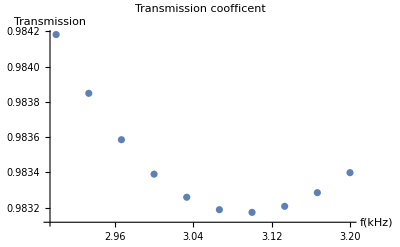

```mathematica
(*Draw the plot*)
ListPlot[Table[{N[f/1000],Tone[f]},{f,fList[noFrequency]}],PlotLabel->"Transmission coofficent",AxesLabel->{"f(kHz)","Transmission"} ]
```

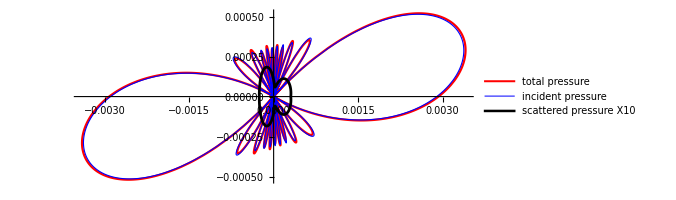

```mathematica
nVal =10;
PolarPlot[{Re[PtotR[100000,ϕ,2900]],Re[PR[100000,ϕ,2900]],10 Re[PscR[100000,ϕ,2900]]},{ϕ,0,2 π},PlotStyle->{Directive[Red,Thickness[0.004]],Directive[Blue,Thickness[0.002]],Directive[Black,Thickness[0.005]]},PlotLegends->{"total pressure","incident pressure","scattered pressure X10"}]
nVal = 100;
```

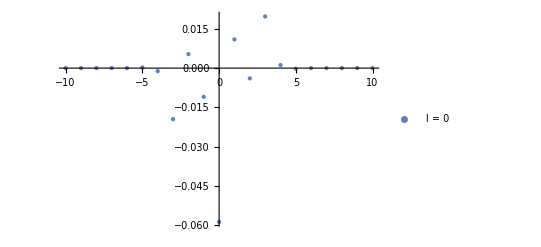

```mathematica
listchain[t_]:=Table[{n,Re[B[t,n,2900]]},{n,-nValue,nValue}];
allLists=Table[listchain[t],{t,-Num,Num}];
ListPlot[allLists,PlotStyle->{PointSize[Large]},PlotLegends->Table["l = "<>ToString[t],{t,-Num,Num}],PlotRange->All]
```

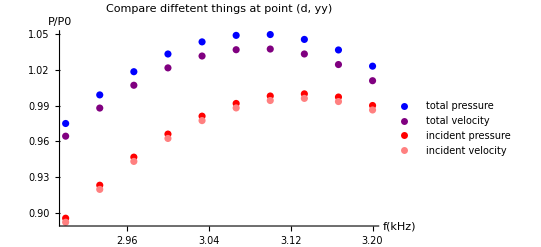

```mathematica
yy = 0;
plot1=ListPlot[Table[{N[f/1000],1/p0 Re[Ptot[d,yy,f]]},{f,fList[noFrequency]}],PlotStyle->Blue,PlotLegends->{"total pressure"}];
plot4=ListPlot[Table[{N[f/1000],1/v0 Re[Vtot[d,yy,f]]},{f,fList[noFrequency]}],PlotStyle->Purple,PlotLegends->{"total velocity"}];
plot2=ListPlot[Table[{N[f/1000],1/p0 Re[P[d,yy,f]]},{f,fList[noFrequency]}],PlotStyle->Red,PlotLegends->{"incident pressure"}];
plot3=ListPlot[Table[{N[f/1000],1/v0 Re[V[d,yy,f]]},{f,fList[noFrequency]}],PlotStyle->Pink,PlotLegends->{"incident velocity"}];
(*Combine the plots using Show*)
Show[{plot1,plot4,plot2,plot3},PlotLabel->"Compare diffetent things at point (d, yy)",AxesLabel->{"f(kHz)","P/P0"},PlotRange->All]
```

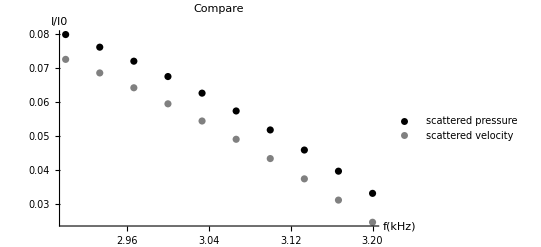

```mathematica
plot1=ListPlot[Table[{N[f/1000],1/p0 Re[Psc[d,yy,f]]},{f,fList[noFrequency]}],PlotStyle->Black,PlotLegends->{"scattered pressure"}];
plot2=ListPlot[Table[{N[f/1000],1/v0 Re[Vsc[d,yy,f]]},{f,fList[noFrequency]}],PlotStyle->Gray,PlotLegends->{"scattered velocity"}];
(*Combine the plots using Show*)
Show[{plot1,plot2},PlotLabel->"Compare",AxesLabel->{"f(kHz)","I/I0"},PlotRange->All]
```

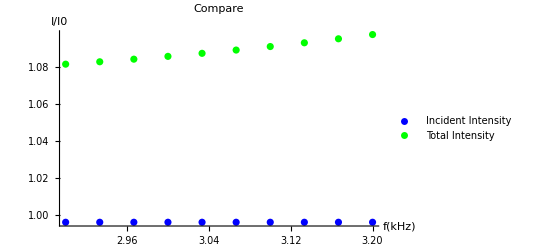

```mathematica
plot1=ListPlot[Table[{N[f/1000],1/(p0 v0)Re[P[d,yy,f]Conjugate[V[d,yy,f]]]},{f,fList[noFrequency]}],PlotStyle->Blue,PlotLegends->{"Incident Intensity"}];
plot2=ListPlot[Table[{N[f/1000],1/(p0 v0)Re[Ptot[d,yy,f]Conjugate[Vtot[d,yy,f]]]},{f,fList[noFrequency]}],PlotStyle->Green,PlotLegends->{"Total Intensity"}];
(*Combine the plots using Show*)
Show[{plot1,plot2},PlotLabel->"Compare",AxesLabel->{"f(kHz)","I/I0"},PlotRange->All]
```

#### 3 cylinder with n<11

```mathematica
(*Transmissopn coofficent*)
noFrequency = 10;
noCylinder = 3;
Num = NoCylinderFrom0[noCylinder];
nValue = 10;

(*Range of Frequency*)
fStart = 2900;
fEnd = 3200;

Clear[B]
SetAttributes[B,Constant]

(*set a range for calculation, the chain and for different modes of scatter*)
nRange=Range[-nValue, nValue];
tRange= Range[-Num, Num];
fList[n_] := Range[fStart,fEnd,(fEnd-fStart)/(n-1)];

(*Calculating sets of constants for each frequency*)
Table[equations=Flatten[Table[eq[n,t,f],{n,nRange},{t,tRange}]];
unknowns=Flatten[Table[B[t,n,f],{n,nRange},{t,tRange}]];
coeffMatrix=CoefficientArrays[equations,unknowns][[2]];
rhsVector=-CoefficientArrays[equations,unknowns][[1]];
solutionVector=LinearSolve[coeffMatrix,rhsVector];
results=Thread[unknowns->solutionVector];
Table[B[t,n,f]=B[t,n,f]/. results,{n,nRange},{t,tRange}],{f,fList[noFrequency]}];
```

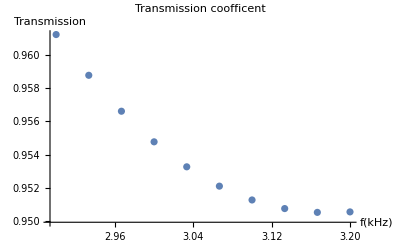

```mathematica
(*Draw the plot*)
ListPlot[Table[{N[f/1000],Tone[f]},{f,fList[noFrequency]}],PlotLabel->"Transmission coofficent",AxesLabel->{"f(kHz)","Transmission"} ]
```

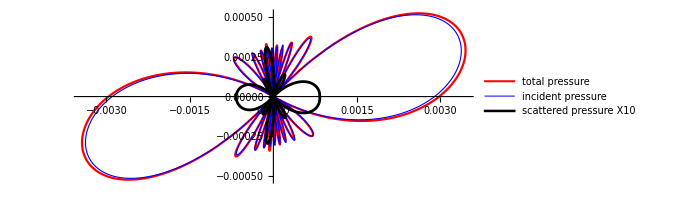

```mathematica
nVal =10;
PolarPlot[{Re[PtotR[100000,ϕ,2900]],Re[PR[100000,ϕ,2900]],10 Re[PscR[100000,ϕ,2900]]},{ϕ,0,2 π},PlotStyle->{Directive[Red,Thickness[0.004]],Directive[Blue,Thickness[0.002]],Directive[Black,Thickness[0.005]]},PlotLegends->{"total pressure","incident pressure","scattered pressure X10"}]
nVal = 100;
```

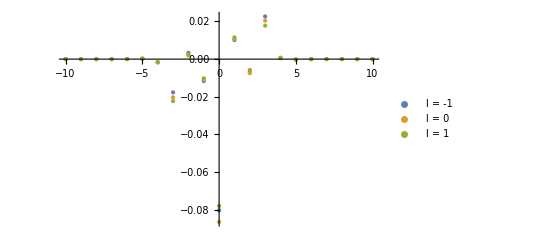

```mathematica
listchain[t_]:=Table[{n,Re[B[t,n,2900]]},{n,-nValue,nValue}];
allLists=Table[listchain[t],{t,-Num,Num}];
ListPlot[allLists,PlotStyle->{PointSize[Large]},PlotLegends->Table["l = "<>ToString[t],{t,-Num,Num}],PlotRange->All]
```

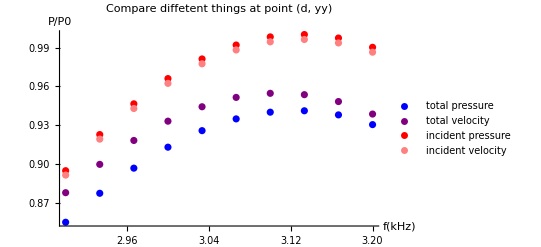

```mathematica
yy = 0;
plot1=ListPlot[Table[{N[f/1000],1/p0 Re[Ptot[d,yy,f]]},{f,fList[noFrequency]}],PlotStyle->Blue,PlotLegends->{"total pressure"}];
plot4=ListPlot[Table[{N[f/1000],1/v0 Re[Vtot[d,yy,f]]},{f,fList[noFrequency]}],PlotStyle->Purple,PlotLegends->{"total velocity"}];
plot2=ListPlot[Table[{N[f/1000],1/p0 Re[P[d,yy,f]]},{f,fList[noFrequency]}],PlotStyle->Red,PlotLegends->{"incident pressure"}];
plot3=ListPlot[Table[{N[f/1000],1/v0 Re[V[d,yy,f]]},{f,fList[noFrequency]}],PlotStyle->Pink,PlotLegends->{"incident velocity"}];
(*Combine the plots using Show*)
Show[{plot1,plot4,plot2,plot3},PlotLabel->"Compare diffetent things at point (d, yy)",AxesLabel->{"f(kHz)","P/P0"},PlotRange->All]
```

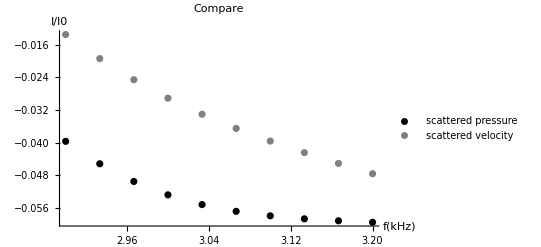

```mathematica
plot1=ListPlot[Table[{N[f/1000],1/p0 Re[Psc[d,yy,f]]},{f,fList[noFrequency]}],PlotStyle->Black,PlotLegends->{"scattered pressure"}];
plot2=ListPlot[Table[{N[f/1000],1/v0 Re[Vsc[d,yy,f]]},{f,fList[noFrequency]}],PlotStyle->Gray,PlotLegends->{"scattered velocity"}];
(*Combine the plots using Show*)
Show[{plot1,plot2},PlotLabel->"Compare",AxesLabel->{"f(kHz)","I/I0"},PlotRange->All]
```

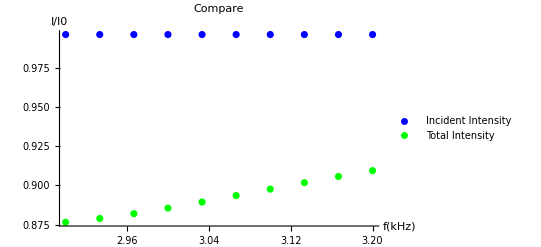

```mathematica
plot1=ListPlot[Table[{N[f/1000],1/(p0 v0)Re[P[d,yy,f]Conjugate[V[d,yy,f]]]},{f,fList[noFrequency]}],PlotStyle->Blue,PlotLegends->{"Incident Intensity"}];
plot2=ListPlot[Table[{N[f/1000],1/(p0 v0)Re[Ptot[d,yy,f]Conjugate[Vtot[d,yy,f]]]},{f,fList[noFrequency]}],PlotStyle->Green,PlotLegends->{"Total Intensity"}];
(*Combine the plots using Show*)
Show[{plot1,plot2},PlotLabel->"Compare",AxesLabel->{"f(kHz)","I/I0"},PlotRange->All]
```

#### 15 cylinder with n<11

```mathematica
(*Transmissopn coofficent*)
noFrequency = 10;
noCylinder = 15;
Num = NoCylinderFrom0[noCylinder];
nValue = 10;

(*Range of Frequency*)
fStart = 2900;
fEnd = 3200;

Clear[B]
SetAttributes[B,Constant]

(*set a range for calculation, the chain and for different modes of scatter*)
nRange=Range[-nValue, nValue];
tRange= Range[-Num, Num];
fList[n_] := Range[fStart,fEnd,(fEnd-fStart)/(n-1)];

(*Calculating sets of constants for each frequency*)
Table[equations=Flatten[Table[eq[n,t,f],{n,nRange},{t,tRange}]];
unknowns=Flatten[Table[B[t,n,f],{n,nRange},{t,tRange}]];
coeffMatrix=CoefficientArrays[equations,unknowns][[2]];
rhsVector=-CoefficientArrays[equations,unknowns][[1]];
solutionVector=LinearSolve[coeffMatrix,rhsVector];
results=Thread[unknowns->solutionVector];
Table[B[t,n,f]=B[t,n,f]/. results,{n,nRange},{t,tRange}],{f,fList[noFrequency]}];
```

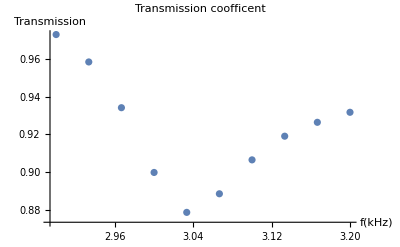

```mathematica
(*Draw the plot*)
ListPlot[Table[{N[f/1000],Tone[f]},{f,fList[noFrequency]}],PlotLabel->"Transmission coofficent",AxesLabel->{"f(kHz)","Transmission"} ]
```

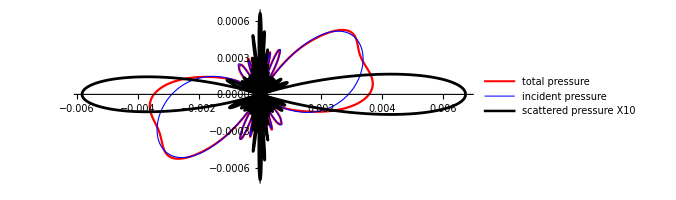

```mathematica
nVal =10;
PolarPlot[{Re[PtotR[100000,ϕ,2900]],Re[PR[100000,ϕ,2900]],10 Re[PscR[100000,ϕ,2900]]},{ϕ,0,2 π},PlotStyle->{Directive[Red,Thickness[0.004]],Directive[Blue,Thickness[0.002]],Directive[Black,Thickness[0.005]]},PlotLegends->{"total pressure","incident pressure","scattered pressure X10"}]
nVal = 100;
```

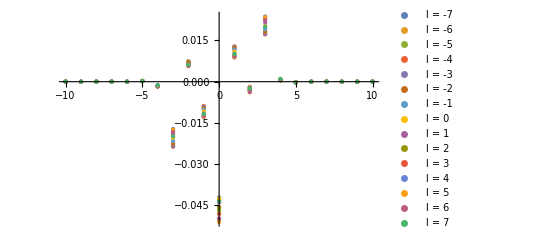

```mathematica
listchain[t_]:=Table[{n,Re[B[t,n,2900]]},{n,-nValue,nValue}];
allLists=Table[listchain[t],{t,-Num,Num}];
ListPlot[allLists,PlotStyle->{PointSize[Large]},PlotLegends->Table["l = "<>ToString[t],{t,-Num,Num}],PlotRange->All]
```

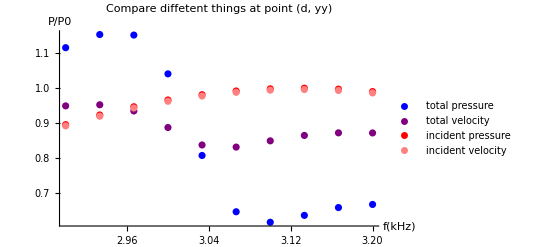

```mathematica
yy = 0;
plot1=ListPlot[Table[{N[f/1000],1/p0 Re[Ptot[d,yy,f]]},{f,fList[noFrequency]}],PlotStyle->Blue,PlotLegends->{"total pressure"}];
plot4=ListPlot[Table[{N[f/1000],1/v0 Re[Vtot[d,yy,f]]},{f,fList[noFrequency]}],PlotStyle->Purple,PlotLegends->{"total velocity"}];
plot2=ListPlot[Table[{N[f/1000],1/p0 Re[P[d,yy,f]]},{f,fList[noFrequency]}],PlotStyle->Red,PlotLegends->{"incident pressure"}];
plot3=ListPlot[Table[{N[f/1000],1/v0 Re[V[d,yy,f]]},{f,fList[noFrequency]}],PlotStyle->Pink,PlotLegends->{"incident velocity"}];
(*Combine the plots using Show*)
Show[{plot1,plot4,plot2,plot3},PlotLabel->"Compare diffetent things at point (d, yy)",AxesLabel->{"f(kHz)","P/P0"},PlotRange->All]
```

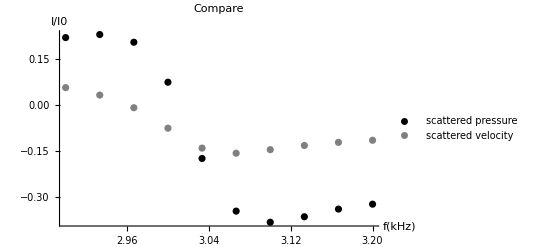

```mathematica
plot1=ListPlot[Table[{N[f/1000],1/p0 Re[Psc[d,yy,f]]},{f,fList[noFrequency]}],PlotStyle->Black,PlotLegends->{"scattered pressure"}];
plot2=ListPlot[Table[{N[f/1000],1/v0 Re[Vsc[d,yy,f]]},{f,fList[noFrequency]}],PlotStyle->Gray,PlotLegends->{"scattered velocity"}];
(*Combine the plots using Show*)
Show[{plot1,plot2},PlotLabel->"Compare",AxesLabel->{"f(kHz)","I/I0"},PlotRange->All]
```

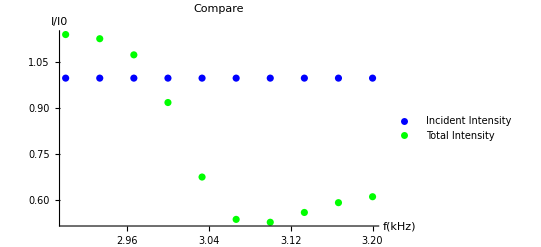

```mathematica
plot1=ListPlot[Table[{N[f/1000],1/(p0 v0)Re[P[d,yy,f]Conjugate[V[d,yy,f]]]},{f,fList[noFrequency]}],PlotStyle->Blue,PlotLegends->{"Incident Intensity"}];
plot2=ListPlot[Table[{N[f/1000],1/(p0 v0)Re[Ptot[d,yy,f]Conjugate[Vtot[d,yy,f]]]},{f,fList[noFrequency]}],PlotStyle->Green,PlotLegends->{"Total Intensity"}];
(*Combine the plots using Show*)
Show[{plot1,plot2},PlotLabel->"Compare",AxesLabel->{"f(kHz)","I/I0"},PlotRange->All]
```

#### 29 cylinder with n<11

```mathematica
(*Transmissopn coofficent*)
noFrequency = 10;
noCylinder = 29;
Num = NoCylinderFrom0[noCylinder];
nValue = 10;

(*Range of Frequency*)
fStart = 2900;
fEnd = 3200;

Clear[B]
SetAttributes[B,Constant]

(*set a range for calculation, the chain and for different modes of scatter*)
nRange=Range[-nValue, nValue];
tRange= Range[-Num, Num];
fList[n_] := Range[fStart,fEnd,(fEnd-fStart)/(n-1)];

(*Calculating sets of constants for each frequency*)
Table[equations=Flatten[Table[eq[n,t,f],{n,nRange},{t,tRange}]];
unknowns=Flatten[Table[B[t,n,f],{n,nRange},{t,tRange}]];
coeffMatrix=CoefficientArrays[equations,unknowns][[2]];
rhsVector=-CoefficientArrays[equations,unknowns][[1]];
solutionVector=LinearSolve[coeffMatrix,rhsVector];
results=Thread[unknowns->solutionVector];
Table[B[t,n,f]=B[t,n,f]/. results,{n,nRange},{t,tRange}],{f,fList[noFrequency]}];
```

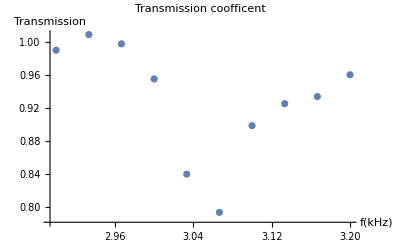

```mathematica
(*Draw the plot*)
ListPlot[Table[{N[f/1000],Tone[f]},{f,fList[noFrequency]}],PlotLabel->"Transmission coofficent",AxesLabel->{"f(kHz)","Transmission"} ]
```

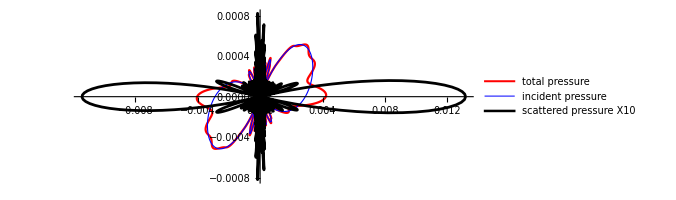

```mathematica
nVal =10;
PolarPlot[{Re[PtotR[100000,ϕ,2900]],Re[PR[100000,ϕ,2900]],10 Re[PscR[100000,ϕ,2900]]},{ϕ,0,2 π},PlotStyle->{Directive[Red,Thickness[0.004]],Directive[Blue,Thickness[0.002]],Directive[Black,Thickness[0.005]]},PlotLegends->{"total pressure","incident pressure","scattered pressure X10"}]
nVal = 100;
```

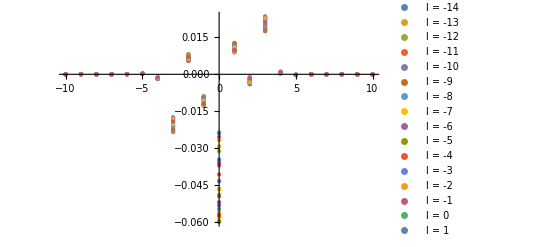

```mathematica
listchain[t_]:=Table[{n,Re[B[t,n,2900]]},{n,-nValue,nValue}];
allLists=Table[listchain[t],{t,-Num,Num}];
ListPlot[allLists,PlotStyle->{PointSize[Large]},PlotLegends->Table["l = "<>ToString[t],{t,-Num,Num}],PlotRange->All]
```

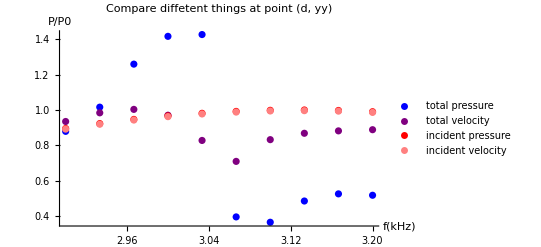

```mathematica
yy = 0;
plot1=ListPlot[Table[{N[f/1000],1/p0 Re[Ptot[d,yy,f]]},{f,fList[noFrequency]}],PlotStyle->Blue,PlotLegends->{"total pressure"}];
plot4=ListPlot[Table[{N[f/1000],1/v0 Re[Vtot[d,yy,f]]},{f,fList[noFrequency]}],PlotStyle->Purple,PlotLegends->{"total velocity"}];
plot2=ListPlot[Table[{N[f/1000],1/p0 Re[P[d,yy,f]]},{f,fList[noFrequency]}],PlotStyle->Red,PlotLegends->{"incident pressure"}];
plot3=ListPlot[Table[{N[f/1000],1/v0 Re[V[d,yy,f]]},{f,fList[noFrequency]}],PlotStyle->Pink,PlotLegends->{"incident velocity"}];
(*Combine the plots using Show*)
Show[{plot1,plot4,plot2,plot3},PlotLabel->"Compare diffetent things at point (d, yy)",AxesLabel->{"f(kHz)","P/P0"},PlotRange->All]
```

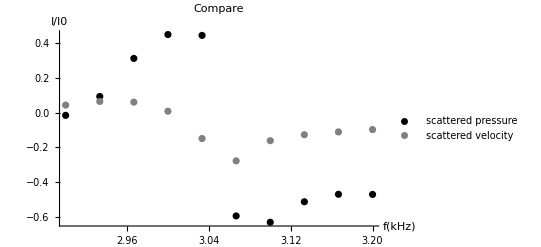

```mathematica
plot1=ListPlot[Table[{N[f/1000],1/p0 Re[Psc[d,yy,f]]},{f,fList[noFrequency]}],PlotStyle->Black,PlotLegends->{"scattered pressure"}];
plot2=ListPlot[Table[{N[f/1000],1/v0 Re[Vsc[d,yy,f]]},{f,fList[noFrequency]}],PlotStyle->Gray,PlotLegends->{"scattered velocity"}];
(*Combine the plots using Show*)
Show[{plot1,plot2},PlotLabel->"Compare",AxesLabel->{"f(kHz)","I/I0"},PlotRange->All]
```

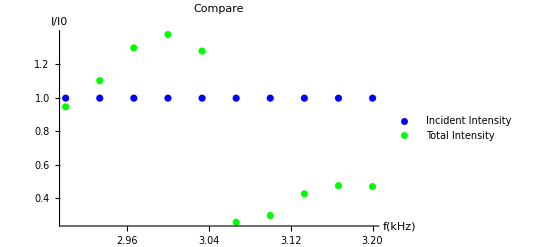

```mathematica
plot1=ListPlot[Table[{N[f/1000],1/(p0 v0)Re[P[d,yy,f]Conjugate[V[d,yy,f]]]},{f,fList[noFrequency]}],PlotStyle->Blue,PlotLegends->{"Incident Intensity"}];
plot2=ListPlot[Table[{N[f/1000],1/(p0 v0)Re[Ptot[d,yy,f]Conjugate[Vtot[d,yy,f]]]},{f,fList[noFrequency]}],PlotStyle->Green,PlotLegends->{"Total Intensity"}];
(*Combine the plots using Show*)
Show[{plot1,plot2},PlotLabel->"Compare",AxesLabel->{"f(kHz)","I/I0"},PlotRange->All]
```

#### 31 cylinder with n<5

```mathematica
(*Transmissopn coofficent*)
noFrequency = 13;
noCylinder = 31;
Num = NoCylinderFrom0[noCylinder];
nValue = 4;

(*Range of Frequency*)
fStart = 2900;
fEnd = 3200;

Clear[B]
SetAttributes[B,Constant]

(*set a range for calculation, the chain and for different modes of scatter*)
nRange=Range[-nValue, nValue];
tRange= Range[-Num, Num];
fList[n_] := Range[fStart,fEnd,(fEnd-fStart)/(n-1)];

(*Calculating sets of constants for each frequency*)
Table[equations=Flatten[Table[eq[n,t,f],{n,nRange},{t,tRange}]];
unknowns=Flatten[Table[B[t,n,f],{n,nRange},{t,tRange}]];
coeffMatrix=CoefficientArrays[equations,unknowns][[2]];
rhsVector=-CoefficientArrays[equations,unknowns][[1]];
solutionVector=LinearSolve[coeffMatrix,rhsVector];
results=Thread[unknowns->solutionVector];
Table[B[t,n,f]=B[t,n,f]/. results,{n,nRange},{t,tRange}],{f,fList[noFrequency]}];
```

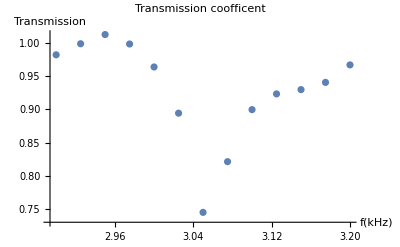

```mathematica
(*Draw the plot*)
ListPlot[Table[{N[f/1000],Tone[f]},{f,fList[noFrequency]}],PlotLabel->"Transmission coofficent",AxesLabel->{"f(kHz)","Transmission"} ]
```

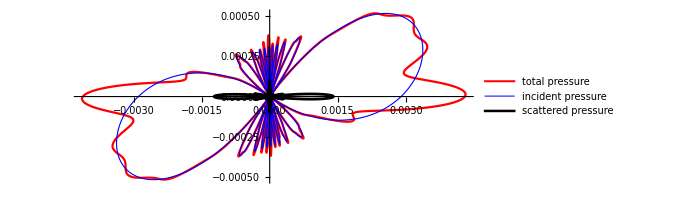

```mathematica
nVal =10;
PolarPlot[{Re[PtotR[100000,ϕ,2900]],Re[PR[100000,ϕ,2900]],Re[PscR[100000,ϕ,2900]]},{ϕ,0,2 π},PlotStyle->{Directive[Red,Thickness[0.004]],Directive[Blue,Thickness[0.002]],Directive[Black,Thickness[0.005]]},PlotLegends->{"total pressure","incident pressure","scattered pressure"}]
nVal = 100;
```

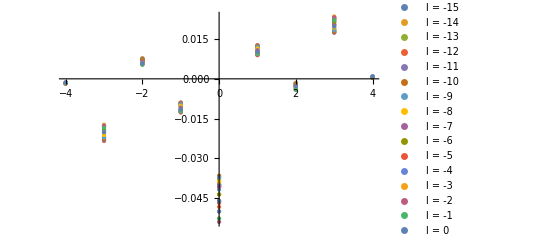

```mathematica
listchain[t_]:=Table[{n,Re[B[t,n,2900]]},{n,-nValue,nValue}];
allLists=Table[listchain[t],{t,-Num,Num}];
ListPlot[allLists,PlotStyle->{PointSize[Large]},PlotLegends->Table["l = "<>ToString[t],{t,-Num,Num}],PlotRange->All]
```

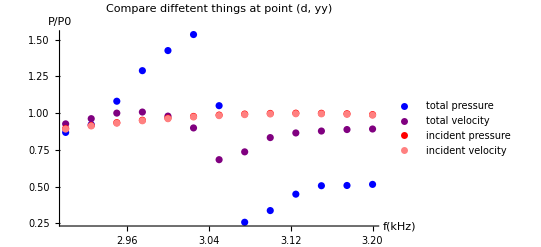

```mathematica
yy = 0;
plot1=ListPlot[Table[{N[f/1000],1/p0 Re[Ptot[d,yy,f]]},{f,fList[noFrequency]}],PlotStyle->Blue,PlotLegends->{"total pressure"}];
plot4=ListPlot[Table[{N[f/1000],1/v0 Re[Vtot[d,yy,f]]},{f,fList[noFrequency]}],PlotStyle->Purple,PlotLegends->{"total velocity"}];
plot2=ListPlot[Table[{N[f/1000],1/p0 Re[P[d,yy,f]]},{f,fList[noFrequency]}],PlotStyle->Red,PlotLegends->{"incident pressure"}];
plot3=ListPlot[Table[{N[f/1000],1/v0 Re[V[d,yy,f]]},{f,fList[noFrequency]}],PlotStyle->Pink,PlotLegends->{"incident velocity"}];
(*Combine the plots using Show*)
Show[{plot1,plot4,plot2,plot3},PlotLabel->"Compare diffetent things at point (d, yy)",AxesLabel->{"f(kHz)","P/P0"},PlotRange->All]
```

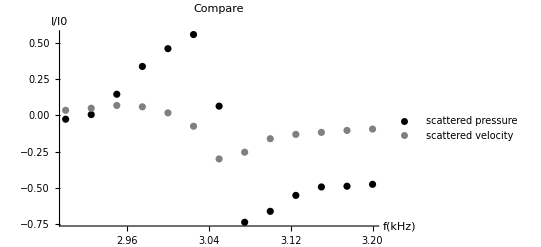

```mathematica
plot1=ListPlot[Table[{N[f/1000],1/p0 Re[Psc[d,yy,f]]},{f,fList[noFrequency]}],PlotStyle->Black,PlotLegends->{"scattered pressure"}];
plot2=ListPlot[Table[{N[f/1000],1/v0 Re[Vsc[d,yy,f]]},{f,fList[noFrequency]}],PlotStyle->Gray,PlotLegends->{"scattered velocity"}];
(*Combine the plots using Show*)
Show[{plot1,plot2},PlotLabel->"Compare",AxesLabel->{"f(kHz)","I/I0"},PlotRange->All]
```

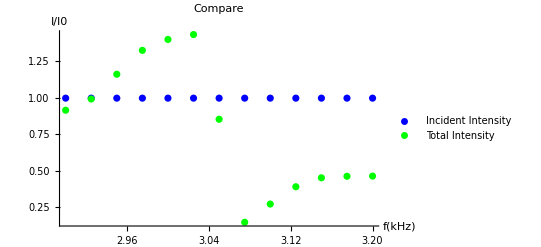

```mathematica
plot1=ListPlot[Table[{N[f/1000],1/(p0 v0)Re[P[d,yy,f]Conjugate[V[d,yy,f]]]},{f,fList[noFrequency]}],PlotStyle->Blue,PlotLegends->{"Incident Intensity"}];
plot2=ListPlot[Table[{N[f/1000],1/(p0 v0)Re[Ptot[d,yy,f]Conjugate[Vtot[d,yy,f]]]},{f,fList[noFrequency]}],PlotStyle->Green,PlotLegends->{"Total Intensity"}];
(*Combine the plots using Show*)
Show[{plot1,plot2},PlotLabel->"Compare",AxesLabel->{"f(kHz)","I/I0"},PlotRange->All]
```

#### 71 cylinder with n<5

```mathematica
(*Transmissopn coofficent*)
noFrequency = 13;
noCylinder = 71;
Num = NoCylinderFrom0[noCylinder];
nValue = 4;

(*Range of Frequency*)
fStart = 3020;
fEnd = 3100;

Clear[B]
SetAttributes[B,Constant]

(*set a range for calculation, the chain and for different modes of scatter*)
nRange=Range[-nValue, nValue];
tRange= Range[-Num, Num];
fList[n_] := Range[fStart,fEnd,(fEnd-fStart)/(n-1)];

(*Calculating sets of constants for each frequency*)
Table[equations=Flatten[Table[eq[n,t,f],{n,nRange},{t,tRange}]];
unknowns=Flatten[Table[B[t,n,f],{n,nRange},{t,tRange}]];
coeffMatrix=CoefficientArrays[equations,unknowns][[2]];
rhsVector=-CoefficientArrays[equations,unknowns][[1]];
solutionVector=LinearSolve[coeffMatrix,rhsVector];
results=Thread[unknowns->solutionVector];
Table[B[t,n,f]=B[t,n,f]/. results,{n,nRange},{t,tRange}],{f,fList[noFrequency]}];
```

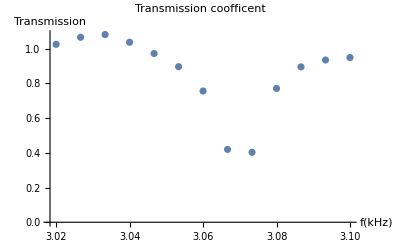

```mathematica
(*Draw the plot*)
ListPlot[Table[{N[f/1000],Tone[f]},{f,fList[noFrequency]}],PlotLabel->"Transmission coofficent",AxesLabel->{"f(kHz)","Transmission"} ]
```

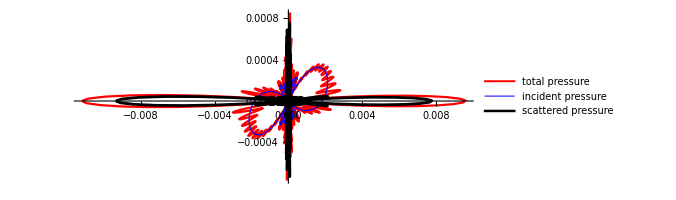

```mathematica
nVal =10;
PolarPlot[{Re[PtotR[100000,ϕ,fStart]],Re[PR[100000,ϕ,fStart]],Re[PscR[100000,ϕ,fStart]]},{ϕ,0,2 π},PlotStyle->{Directive[Red,Thickness[0.004]],Directive[Blue,Thickness[0.002]],Directive[Black,Thickness[0.005]]},PlotLegends->{"total pressure","incident pressure","scattered pressure"}]
nVal = 100;
```

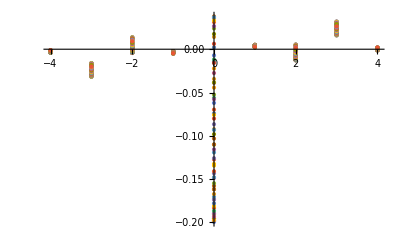

```mathematica
listchain[t_]:=Table[{n,Re[B[t,n,fStart]]},{n,-nValue,nValue}];
allLists=Table[listchain[t],{t,-Num,Num}];
ListPlot[allLists,PlotStyle->{PointSize[Large]},PlotRange->All]
```

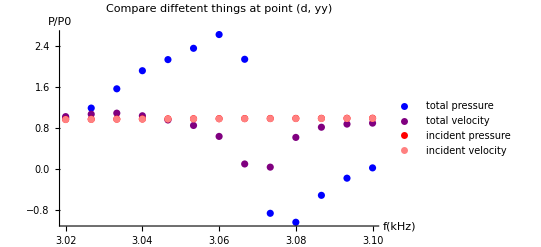

```mathematica
yy = 0;
plot1=ListPlot[Table[{N[f/1000],1/p0 Re[Ptot[d,yy,f]]},{f,fList[noFrequency]}],PlotStyle->Blue,PlotLegends->{"total pressure"}];
plot4=ListPlot[Table[{N[f/1000],1/v0 Re[Vtot[d,yy,f]]},{f,fList[noFrequency]}],PlotStyle->Purple,PlotLegends->{"total velocity"}];
plot2=ListPlot[Table[{N[f/1000],1/p0 Re[P[d,yy,f]]},{f,fList[noFrequency]}],PlotStyle->Red,PlotLegends->{"incident pressure"}];
plot3=ListPlot[Table[{N[f/1000],1/v0 Re[V[d,yy,f]]},{f,fList[noFrequency]}],PlotStyle->Pink,PlotLegends->{"incident velocity"}];
(*Combine the plots using Show*)
Show[{plot1,plot4,plot2,plot3},PlotLabel->"Compare diffetent things at point (d, yy)",AxesLabel->{"f(kHz)","P/P0"},PlotRange->All]
```

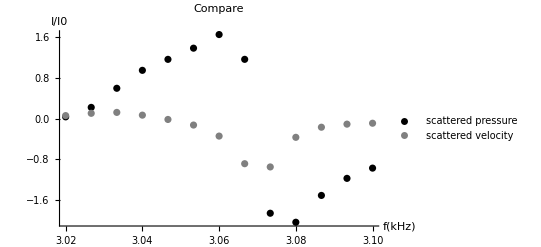

```mathematica
plot1=ListPlot[Table[{N[f/1000],1/p0 Re[Psc[d,yy,f]]},{f,fList[noFrequency]}],PlotStyle->Black,PlotLegends->{"scattered pressure"}];
plot2=ListPlot[Table[{N[f/1000],1/v0 Re[Vsc[d,yy,f]]},{f,fList[noFrequency]}],PlotStyle->Gray,PlotLegends->{"scattered velocity"}];
(*Combine the plots using Show*)
Show[{plot1,plot2},PlotLabel->"Compare",AxesLabel->{"f(kHz)","I/I0"},PlotRange->All]
```

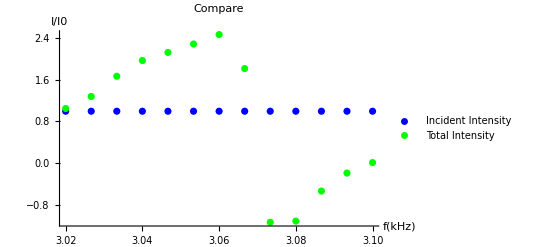

```mathematica
plot1=ListPlot[Table[{N[f/1000],1/(p0 v0)Re[P[d,yy,f]Conjugate[V[d,yy,f]]]},{f,fList[noFrequency]}],PlotStyle->Blue,PlotLegends->{"Incident Intensity"}];
plot2=ListPlot[Table[{N[f/1000],1/(p0 v0)Re[Ptot[d,yy,f]Conjugate[Vtot[d,yy,f]]]},{f,fList[noFrequency]}],PlotStyle->Green,PlotLegends->{"Total Intensity"}];
(*Combine the plots using Show*)
Show[{plot1,plot2},PlotLabel->"Compare",AxesLabel->{"f(kHz)","I/I0"},PlotRange->All]
```